## 03 Ball on the Ramp

As in the diagram shown below, a ball with mass m=0.50kg lies on a fictionless ramp with angle θ=30°.

-Graphics-

When the ramp moves at the acceleration a=2.0m/s^2 as in the diagram, what’s the tension of the string and the nomal force exerted on the ball by the ramp?

T=ma cos(θ)+mg sin(θ)

```mathematica
0.5(√3+9.8/2)
```

3.31603

N=mg cos(θ)-ma sin(θ)

```mathematica
0.5(9.8√3/2-1)
```

3.74352

What’s the minimum acceleration such that the ball will leave the ramp?

N=mg cos(θ)-ma sin(θ)=0
a=g cot(θ)

```mathematica
9.8 √3
```

16.9741

## 04 Ball inside the Ring

A ring with radius R=1m is fixed on a frictionless table. A point particle moves along the inner side, as shown below. The coefficient of kinetic friction bettween the particle and the ring is μ_k=0.5 and the speed of the particle is v_0=2m/s when passing the point A.

-Graphics-

What’s the speed of the particle when t=2s?

a⃗=ⅆv/ⅆt θ̂-v^2/r r̂
ⅆv/ⅆt=-μ_k v^2/r⇒ⅆv/v^2=-μ_k/rⅆt⇒1/v=(μ_k t+C)/r
v=r/(μ_k t+C)

```mathematica
r=1;Subscript[μ, k]=1/2;Subscript[v, 0]=2;
Clear[v];
DSolve[v'[t]==-Subscript[μ, k] v[t]^2/r&&v[0]==Subscript[v, 0],v,t];
```

```mathematica
v[t_]=v[t]/.%[[1]]
```

2/(1+t)

```mathematica
v[2.0]
```

0.666667

What’s the distance traveled by the particle at this time?

∫_0^2 v(t)ⅆt=2 ∫_1^3 1/u ⅆu=2log(3)≈2.19722

## 05 The lurking peril of braking suddenly

When braking, the truck moves with a constant deceleration a=7.0m/s^2. A box on the back of the truck, originally at rest, begins to slide as soon as the truck brakes. After sliding a distance of l=2m, the box bumps into the cabin. The coefficient of kinetic friction between the box and carge bed is μ_k=0.50 . What’s the speed of the box when it hits the cabin (as observed in the truck reference frame)?

∫_0^t_0 (a-μ_k g)tⅆt=2⇒1/2(a-μ_k g)t^2=2

```mathematica
a=7;l=2;Subscript[μ, k]=0.5;g=9.8;
Solve[1/2(a-Subscript[μ, k] g)t^2==l&&t>0,Reals]
```

{{t→1.38013}}

```mathematica
(a-Subscript[μ, k] g)t/.%[[1]]
```

2.89828

## 06 Impulse

A ball with mass m=50g travels in uniform circular motion at the speed of v=20m/s. What’s the impulse during one quarter of the period?

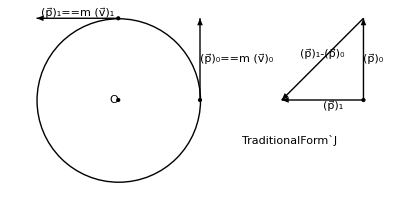

```mathematica
Graphics[{Circle[],Point[{{0,0},{1,0},{0,1},{3,0}}],
Arrowheads[Small],Text[O,{0,0},{2,0}],
Arrow[{{1,0},{1,1}}],Arrow[{{0,1},{-1,1}}],
Text[Subscript[p⃗, 0]==m Subscript[v⃗, 0],{1,0.5},{-1.2,0}],Text[Subscript[p⃗, 1]==m Subscript[v⃗, 1],{-.5,1},{0,-1.5}],
Arrow[{{3,0},{3,1}}],Arrow[{{3,0},{2,0}}],
Arrow[{{3,1},{2,0}}],Text[Subscript[p⃗, 1]-Subscript[p⃗, 0],{2.5,0.5},{0,-1.7},{1,1}],
Text[Subscript[p⃗, 1],{2.5,0},{-1,1.5}],
Text[Subscript[p⃗, 0],{3,.5},{-1.75,0}],
Text[Style["TraditionalForm`J",Medium],{2.1,-.5}]}]
```

```mathematica
m=50;v=20;√2 m v//N
```

1414.21

## 07 Chain

On the table lies a long and soft chain, the end of which is pulled up at a constant speed v_0. What’s the pulling force F when the pulled-up part has the length l?

∫_0^t (F-ρlg)ⅆt=ρl v_0⇒ⅆ/ⅆt∫_0^t (F-ρlg)ⅆt=ⅆ/ⅆt ρl v_0
F-ρlg=ρ v_0^2⇒F=ρlg+ρ v_0^2

## 08 Radiocative Decay

During radiocative decay, an originally static atomic nucleus releases an electron with momentum p_1=9.22units and a neutrino with momentum p_2=5.33 units in the direction orthogonal to the electron. (1 unit=10^-21 kg·m/s) What’s the momentum of the nucleus after the decay and the angle between its direction and that of the electron?

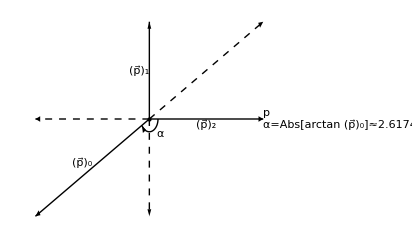

```mathematica
Subscript[p, 1]=9.22;Subscript[p, 2]=5.33;Subscript[p, 0]=√(Subscript[p, 1]^2+Subscript[p, 2]^2);
pt0={0,0};pt1={0,Subscript[p, 2]};pt2={Subscript[p, 1],0};pt3=-(pt1+pt2);
α=ArcTan@@pt3;
Graphics[{Point[pt0],Arrow[{pt0,pt1}],
Arrow[{pt0,pt2}],Arrow[{pt0,pt3}],
Dashed,Arrow[{pt0,-pt1}],Arrow[{pt0,-pt2}],
Arrow[{pt0,-pt3}],
Text[Grid[{{"p"},
{"α=Abs[arctan (p⃗)_0]≈2.61744"}},Alignment->"",ItemStyle->Medium],pt2,{-1.5,0}],
Text[Subscript[p⃗, 1],pt1/2,{1.5,0}],
Text[Subscript[p⃗, 2],pt2/2,{0,1.5}],
Text[Subscript[p⃗, 0],pt3/2,{1,-1.5}],
Thin,Dashing[{}],Arrowheads[Tiny],Arrow@BezierCurve@Table[{.7Cos[t],.7Sin[t]},{t,0,α,-.05}],
Text["α",{r Cos[t],r Sin[t]}/.{r->1.2,t->-π/4}]}]
```

## 09 Jet Aircraft

A jet aircraft travels at 210 m/s. The free stream air is brought into the engine at 75kg/s and then mixed  and burned with the 3kg fuel. The exhaust gases comes out the nozzle at 490m/s. What’s the thrust produced by the exhaust gases?

(ⅆ p⃗)/ⅆt=Ṁ v+M v̇+ṁ (v-u)=0⇒F_thr=M v̇=-Ṁv+ṁ(u-v)=22470

```mathematica
Ṁ=-3;ṁ=75-(-3);v=210;u=490;
-Ṁ v+ṁ(u-v)
```

22470